## Diffusion–Reaction

```mathematica
sizes={53,185,689,2657,10433,41345,164609,656897};
mgv={.025,.029,.035,.079,.222,.864,3.896,16.174};
mgw={.018,.034,.05,.111,.385,1.094,5.332,20.045};
pcg={.024,.032,.045,.077,.224,.826,2.858,12.907};
cg={.007,.024,.031,.14,.859,6.295,73.931,605.463};
lucg={.032,.033,.039,.064,.267,4.494,47.535,359.752};
```

```mathematica
mgv=Table[{sizes[[i]],mgv[[i]]},{i,8}];
mgw=Table[{sizes[[i]],mgw[[i]]},{i,8}];
pcg=Table[{sizes[[i]],pcg[[i]]},{i,8}];
cg=Table[{sizes[[i]],cg[[i]]},{i,8}];
lucg=Table[{sizes[[i]],lucg[[i]]},{i,8}];
```

```mathematica
ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

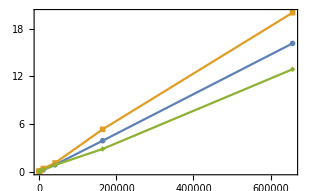
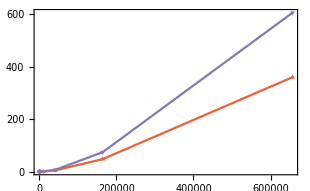

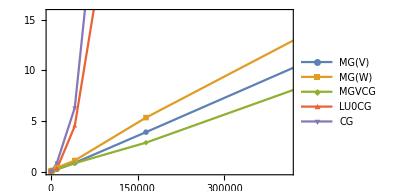

```mathematica
Row[{
ListLinePlot[{mgv,mgw,pcg},PlotMarkers->{Automatic,Medium},Frame->True,PlotRange->All,ImageSize->310],
ListLinePlot[{lucg,cg},Frame->True,PlotMarkers->{{"▲",Medium},{"▼",Medium}},ImageSize->310,PlotRange->All,PlotStyle->ColorData[97,"ColorList"][[4;;]]]
},"    "]
ListLinePlot[{mgv,mgw,pcg,lucg,cg},PlotMarkers->{Automatic,Medium},ClippingStyle->False,Frame->True,PlotLegends->Placed[{"MG(V)","MG(W)","MGVCG","LU0CG","CG"},Right],ImageSize->310,PlotStyle->ColorData[97,"ColorList"]]
```

```mathematica
Graphics`PlotMarkers[]
```

## Magnetostatic Poisson